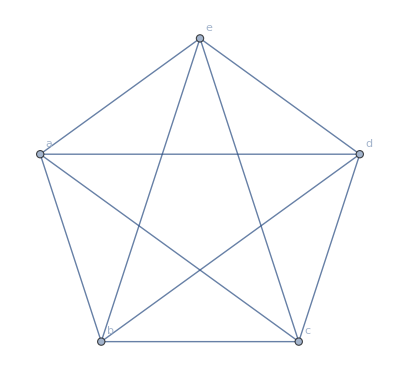

```mathematica
CompleteGraph[5,VertexLabels->Table[k->{a,b,c,d,e}[[k]],{k,5}]]
```

```mathematica
crit1=((a==c)&&(b==d))||((a==c)&&(b!=d)&&(a!=c)&&(b==d))
```

(a==c&&b==d)||(a==c&&b≠d&&a≠c&&b==d)

```mathematica
Reduce[crit1]
```

b==d&&a==c

```mathematica
crit2=crit1/.{a->b,b->c,c->d,d->e}
```

(b==d&&c==e)||(b==d&&c≠e&&b≠d&&c==e)

```mathematica
crit3=crit1/.{a->c,b->d,c->e,d->a}
```

(c==e&&d==a)||(c==e&&d≠a&&c≠e&&d==a)

```mathematica
crit4=crit1/.{a->d,b->e,c->a,d->b}
```

(d==a&&e==b)||(d==a&&e≠b&&d≠a&&e==b)

```mathematica
crit5=crit1/.{a->e,b->a,c->b,d->c}
```

(e==b&&a==c)||(e==b&&a≠c&&e≠b&&a==c)

```mathematica
ListofVars[crit1]//Tally//Sort
```

{{a,3},{b,3},{c,3},{d,3}}

```mathematica
crit1&&crit2&&crit3&&crit4&&crit5//Simplify
```

a==c&&b==d&&c==e&&a==d&&b==e

## Second try

```mathematica
crit1=(((a==c)||(b==d))||((a==c)&&(b==d)))//Simplify
```

a==c||b==d

```mathematica
Reduce[crit1]
```

a==c||b==d

```mathematica
crit2=crit1/.{a->b,b->c,c->d,d->e}
```

b==d||c==e

```mathematica
crit3=crit1/.{a->c,b->d,c->e,d->a}
```

c==e||d==a

```mathematica
crit4=crit1/.{a->d,b->e,c->a,d->b}
```

d==a||e==b

```mathematica
crit5=crit1/.{a->e,b->a,c->b,d->c}
```

e==b||a==c

```mathematica
ListofVars[crit1]//Tally//Sort
```

{{a,1},{b,1},{c,1},{d,1}}

```mathematica
crit1&&crit2&&crit3&&crit4&&crit5//BooleanMinimize
```

(a==c&&b==d&&d==a)||(a==c&&c==e&&d==a)||(a==c&&c==e&&e==b)||(b==d&&c==e&&e==b)||(b==d&&d==a&&e==b)

```mathematica
BooleanConvert[crit1&&crit2&&crit3&&crit4&&crit5,"DNF"]
```

(a==c&&b==d&&d==a)||(a==c&&c==e&&d==a)||(a==c&&c==e&&e==b)||(b==d&&c==e&&e==b)||(b==d&&d==a&&e==b)

```mathematica
BooleanConvert[crit1&&crit2&&crit3&&crit4&&crit5,"AND"]
```

!(a≠c&&b≠d)&&!(a≠c&&e≠b)&&!(b≠d&&c≠e)&&!(c≠e&&d≠a)&&!(d≠a&&e≠b)

```mathematica
BooleanConvert[crit1&&crit2&&crit3&&crit4&&crit5,"OR"]
```

!(a≠c||b≠d||d≠a)||!(a≠c||c≠e||d≠a)||!(a≠c||c≠e||e≠b)||!(b≠d||c≠e||e≠b)||!(b≠d||d≠a||e≠b)

```mathematica
BooleanConvert[crit1&&crit2&&crit3&&crit4&&crit5,"ESOP"]
```

(b==d&&d==a&&e==b)⊻(a==c&&c==e&&d==a&&e≠b)⊻(a==c&&b≠d&&c==e&&e==b)⊻(b==d&&c==e&&d≠a&&e==b)⊻(a==c&&b==d&&c≠e&&d==a&&e≠b)

```mathematica
Magnify[BooleanConvert[crit1&&crit2&&crit3&&crit4&&crit5,"DNF"]//ExpressionToList//TableForm//TraditionalForm,2]/.{a->Red,b->Green,c->Blue,d->Yellow,e->Orange}
```

RGBColor[1, 0, 0]==RGBColor[0, 0, 1]∧RGBColor[0, 1, 0]==RGBColor[1, 1, 0]∧RGBColor[1, 1, 0]==RGBColor[1, 0, 0]
RGBColor[1, 0, 0]==RGBColor[0, 0, 1]∧RGBColor[0, 0, 1]==RGBColor[1, 0.5, 0]∧RGBColor[1, 1, 0]==RGBColor[1, 0, 0]
RGBColor[1, 0, 0]==RGBColor[0, 0, 1]∧RGBColor[0, 0, 1]==RGBColor[1, 0.5, 0]∧RGBColor[1, 0.5, 0]==RGBColor[0, 1, 0]
RGBColor[0, 1, 0]==RGBColor[1, 1, 0]∧RGBColor[0, 0, 1]==RGBColor[1, 0.5, 0]∧RGBColor[1, 0.5, 0]==RGBColor[0, 1, 0]
RGBColor[0, 1, 0]==RGBColor[1, 1, 0]∧RGBColor[1, 1, 0]==RGBColor[1, 0, 0]∧RGBColor[1, 0.5, 0]==RGBColor[0, 1, 0]

```mathematica
Table[ShowGraph5Least[k,"colofour"],{k,Select[allGraphs5AtomKeys,2<VertexCount[allGraphs5[#,"graph"]]<5&]}]
```

{-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ⊙
■ | ■ | ■ | ⊙ | ⊙)v1x2x3x45,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ■ | ⊙
■ | ■ | ■ | ⊙ | ■
■ | ■ | ⊙ | ■ | ⊙)v1x2x35x4,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ⊙ | ■
■ | ■ | ⊙ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v1x2x34x5,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ⊙ | ⊙
■ | ■ | ⊙ | ⊙ | ⊙
■ | ■ | ⊙ | ⊙ | ⊙)v1x2x345,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ■ | ■ | ⊙
■ | ■ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ■
■ | ⊙ | ■ | ■ | ⊙)v1x25x3x4,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ■ | ■ | ⊙
■ | ■ | ⊙ | ⊙ | ■
■ | ■ | ⊙ | ⊙ | ■
■ | ⊙ | ■ | ■ | ⊙)v1x25x34,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ■ | ⊙ | ■
■ | ■ | ⊙ | ■ | ■
■ | ⊙ | ■ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v1x24x3x5,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ■ | ⊙ | ■
■ | ■ | ⊙ | ■ | ⊙
■ | ⊙ | ■ | ⊙ | ■
■ | ■ | ⊙ | ■ | ⊙)v1x24x35,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ■ | ⊙ | ⊙
■ | ■ | ⊙ | ■ | ■
■ | ⊙ | ■ | ⊙ | ⊙
■ | ⊙ | ■ | ⊙ | ⊙)v1x245x3,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ⊙ | ■ | ■
■ | ⊙ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v1x23x4x5,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ⊙ | ■ | ■
■ | ⊙ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ⊙
■ | ■ | ■ | ⊙ | ⊙)v1x23x45,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ⊙ | ■ | ⊙
■ | ⊙ | ⊙ | ■ | ⊙
■ | ■ | ■ | ⊙ | ■
■ | ⊙ | ⊙ | ■ | ⊙)v1x235x4,-Graphics-(⊙ | ■ | ■ | ■ | ■
■ | ⊙ | ⊙ | ⊙ | ■
■ | ⊙ | ⊙ | ⊙ | ■
■ | ⊙ | ⊙ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v1x234x5,-Graphics-(⊙ | ■ | ■ | ■ | ⊙
■ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ■
⊙ | ■ | ■ | ■ | ⊙)v15x2x3x4,-Graphics-(⊙ | ■ | ■ | ■ | ⊙
■ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ⊙ | ■
■ | ■ | ⊙ | ⊙ | ■
⊙ | ■ | ■ | ■ | ⊙)v15x2x34,-Graphics-(⊙ | ■ | ■ | ■ | ⊙
■ | ⊙ | ■ | ⊙ | ■
■ | ■ | ⊙ | ■ | ■
■ | ⊙ | ■ | ⊙ | ■
⊙ | ■ | ■ | ■ | ⊙)v15x24x3,-Graphics-(⊙ | ■ | ■ | ■ | ⊙
■ | ⊙ | ⊙ | ■ | ■
■ | ⊙ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ■
⊙ | ■ | ■ | ■ | ⊙)v15x23x4,-Graphics-(⊙ | ■ | ■ | ⊙ | ■
■ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ■ | ■
⊙ | ■ | ■ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v14x2x3x5,-Graphics-(⊙ | ■ | ■ | ⊙ | ■
■ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ■ | ⊙
⊙ | ■ | ■ | ⊙ | ■
■ | ■ | ⊙ | ■ | ⊙)v14x2x35,-Graphics-(⊙ | ■ | ■ | ⊙ | ■
■ | ⊙ | ■ | ■ | ⊙
■ | ■ | ⊙ | ■ | ■
⊙ | ■ | ■ | ⊙ | ■
■ | ⊙ | ■ | ■ | ⊙)v14x25x3,-Graphics-(⊙ | ■ | ■ | ⊙ | ■
■ | ⊙ | ⊙ | ■ | ■
■ | ⊙ | ⊙ | ■ | ■
⊙ | ■ | ■ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v14x23x5,-Graphics-(⊙ | ■ | ■ | ⊙ | ⊙
■ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ■ | ■
⊙ | ■ | ■ | ⊙ | ⊙
⊙ | ■ | ■ | ⊙ | ⊙)v145x2x3,-Graphics-(⊙ | ■ | ⊙ | ■ | ■
■ | ⊙ | ■ | ■ | ■
⊙ | ■ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v13x2x4x5,-Graphics-(⊙ | ■ | ⊙ | ■ | ■
■ | ⊙ | ■ | ■ | ■
⊙ | ■ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ⊙
■ | ■ | ■ | ⊙ | ⊙)v13x2x45,-Graphics-(⊙ | ■ | ⊙ | ■ | ■
■ | ⊙ | ■ | ■ | ⊙
⊙ | ■ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ■
■ | ⊙ | ■ | ■ | ⊙)v13x25x4,-Graphics-(⊙ | ■ | ⊙ | ■ | ■
■ | ⊙ | ■ | ⊙ | ■
⊙ | ■ | ⊙ | ■ | ■
■ | ⊙ | ■ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v13x24x5,-Graphics-(⊙ | ■ | ⊙ | ■ | ⊙
■ | ⊙ | ■ | ■ | ■
⊙ | ■ | ⊙ | ■ | ⊙
■ | ■ | ■ | ⊙ | ■
⊙ | ■ | ⊙ | ■ | ⊙)v135x2x4,-Graphics-(⊙ | ■ | ⊙ | ⊙ | ■
■ | ⊙ | ■ | ■ | ■
⊙ | ■ | ⊙ | ⊙ | ■
⊙ | ■ | ⊙ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v134x2x5,-Graphics-(⊙ | ⊙ | ■ | ■ | ■
⊙ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v12x3x4x5,-Graphics-(⊙ | ⊙ | ■ | ■ | ■
⊙ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ⊙
■ | ■ | ■ | ⊙ | ⊙)v12x3x45,-Graphics-(⊙ | ⊙ | ■ | ■ | ■
⊙ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ■ | ⊙
■ | ■ | ■ | ⊙ | ■
■ | ■ | ⊙ | ■ | ⊙)v12x35x4,-Graphics-(⊙ | ⊙ | ■ | ■ | ■
⊙ | ⊙ | ■ | ■ | ■
■ | ■ | ⊙ | ⊙ | ■
■ | ■ | ⊙ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v12x34x5,-Graphics-(⊙ | ⊙ | ■ | ■ | ⊙
⊙ | ⊙ | ■ | ■ | ⊙
■ | ■ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ■
⊙ | ⊙ | ■ | ■ | ⊙)v125x3x4,-Graphics-(⊙ | ⊙ | ■ | ⊙ | ■
⊙ | ⊙ | ■ | ⊙ | ■
■ | ■ | ⊙ | ■ | ■
⊙ | ⊙ | ■ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v124x3x5,-Graphics-(⊙ | ⊙ | ⊙ | ■ | ■
⊙ | ⊙ | ⊙ | ■ | ■
⊙ | ⊙ | ⊙ | ■ | ■
■ | ■ | ■ | ⊙ | ■
■ | ■ | ■ | ■ | ⊙)v123x4x5}

## Trying with 5-atoms

```mathematica
crit1=
```